## Haldane Model

Based on the links:
1) https://topocondmat.org/w4_haldane/haldane_model.html
2) https://phyx.readthedocs.io/en/latest/TI/Lecture%20notes/3.html#haldane-model

### Initialization cells

nearest neighbor vectors

```mathematica
a:={{1,0},{-1/2,(√3)/2},{-1/2,(-√3)/2}}
```

chiral complex hopping vectors

```mathematica
b:={{0,√3},{-3/2,(-√3)/2},{3/2,(-√3)/2}}
```

k vector

```mathematica
k:={kx,ky}
```

### Single-particle spectrum for single-layer graphene

From the structure factor

```mathematica
t1=1;
f=FullSimplify[Sum[Exp[ⅈ k.a[[n]]],{n,1,3}],Assumptions->{kx∈Reals,ky∈Reals}]
Plot3D[{t1 Abs[f],-t1 Abs[f]},{kx,-π,π},{ky,-π,π}, AxesLabel->{"kx","ky","E"}, BoxRatios->Automatic]
```

ⅇ^(-1/2 ⅈ (kx+√3 ky)) (1+ⅇ^(ⅈ √3 ky)+ⅇ^(1/2 ⅈ (3 kx+√3 ky)))

-Graphics3D-

From the Hamiltonian

```mathematica
t1=1;
H=FullSimplify[Sum[t1 Cos[k.a[[n]]]PauliMatrix[1]-t1 Sin[k.a[[n]]]PauliMatrix[2],{n,1,3}],Assumptions->{kx∈Reals,ky∈Reals}]
h1=Eigenvalues[H][[1]];
h2=Eigenvalues[H][[2]];
Plot3D[{h1,h2},{kx,-π,π},{ky,-π,π}, AxesLabel->{"kx","ky","E"}, BoxRatios->Automatic]
```

{{0,ⅇ^(ⅈ kx)+2 ⅇ^(-(ⅈ kx)/2) Cos[(√3 ky)/2]},{Cos[kx]+2 ⅇ^((ⅈ kx)/2) Cos[(√3 ky)/2]-ⅈ Sin[kx],0}}

-Graphics3D-

### Single-particle spectrum for single-layer graphene (along the K->-K line)

#### Check where the points are

```mathematica
Show[Plot3D[{t1 Abs[f],-t1 Abs[f]},{kx,-π,π},{ky,-π,π}, AxesLabel->{"kx","ky","E"}, BoxRatios->Automatic,PlotStyle->Opacity[0.3]],Graphics3D[{Red,PointSize[0.1],Point[{(2π)/3,(2π)/(3 √3),0}],Point[{(-2π)/3,(-2π)/(3 √3),0}]}]]
```

-Graphics3D-

#### Diagonalize the high-symmetry matrix

```mathematica
H=FullSimplify[Sum[t1 Cos[k.a[[n]]]PauliMatrix[1]-t1 Sin[k.a[[n]]]PauliMatrix[2],{n,1,3}],Assumptions->{kx∈Reals,ky∈Reals}]
```

{{0,ⅇ^(ⅈ kx)+2 ⅇ^(-(ⅈ kx)/2) Cos[(√3 ky)/2]},{Cos[kx]+2 ⅇ^((ⅈ kx)/2) Cos[(√3 ky)/2]-ⅈ Sin[kx],0}}

```mathematica
Hnew=H/.ky->kx/(√3)
```

{{0,ⅇ^(ⅈ kx)+2 ⅇ^(-(ⅈ kx)/2) Cos[kx/2]},{2 ⅇ^((ⅈ kx)/2) Cos[kx/2]+Cos[kx]-ⅈ Sin[kx],0}}

```mathematica
h1new=Eigenvalues[Hnew][[1]]
```

-ⅇ^(-ⅈ kx) (1+ⅇ^(ⅈ kx)+ⅇ^(2 ⅈ kx))

```mathematica
h2new=Eigenvalues[Hnew][[2]]
```

ⅇ^(-ⅈ kx) (1+ⅇ^(ⅈ kx)+ⅇ^(2 ⅈ kx))

```mathematica
FullSimplify[h1new,Assumptions->{kx∈Reals,ky∈Reals}]
```

-1-2 Cos[kx]

```mathematica
FullSimplify[h2new,Assumptions->{kx∈Reals,ky∈Reals}]
```

1+2 Cos[kx]

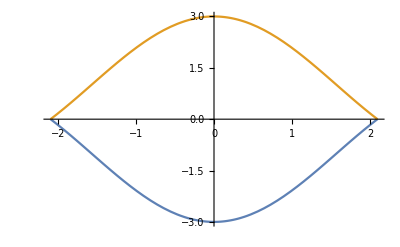

```mathematica
Plot[{-1-2 Cos[kx],1+2 Cos[kx]},{kx,-(2π)/3,(2π)/3}]
```

#### Plot along the high-symmetry line

```mathematica
ComplexExpand[t1 Abs[f]]
```

√((1+Cos[√3 ky]+Cos[1/2 (3 kx+√3 ky)])^2+(Sin[√3 ky]+Sin[1/2 (3 kx+√3 ky)])^2)

```mathematica
Minimize[{√((1+Cos[√3 ky]+Cos[1/2 (3 kx+√3 ky)])^2+(Sin[√3 ky]+Sin[1/2 (3 kx+√3 ky)])^2),-π<kx<π,-π<ky<π},{kx,ky}]
```

{0,{kx→(2 π)/3,ky→(2 π)/(3 √3)}}

```mathematica
√((1+Cos[√3 ky]+Cos[1/2 (3 kx+√3 ky)])^2+(Sin[√3 ky]+Sin[1/2 (3 kx+√3 ky)])^2)/.ky->kx/(√3)
```

```mathematica
√((1+Cos[kx]+Cos[2 kx])^2+(Sin[kx]+Sin[2 kx])^2)
```

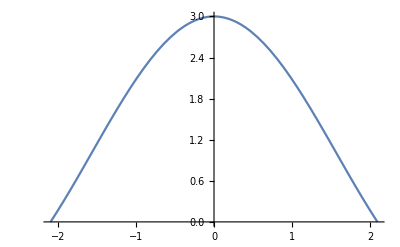

```mathematica
Plot[√((1+Cos[kx]+Cos[2 kx])^2+(Sin[kx]+Sin[2 kx])^2),{kx,-(2π)/3,(2π)/3}]
```

### Adding the Haldane term to the Hamiltonian (with imaginary hopping)

```mathematica
t1=1;
M=0;
t2=0.21;
H=FullSimplify[Sum[t1 Cos[k.a[[n]]]PauliMatrix[1]-t1 Sin[k.a[[n]]]PauliMatrix[2]+2*t2*Sin[k.b[[n]]]PauliMatrix[3],{n,1,3}]+M*PauliMatrix[3],Assumptions->{kx∈Reals,ky∈Reals}]
h1=Eigenvalues[H][[1]];
h2=Eigenvalues[H][[2]];
Plot3D[{h1,h2},{kx,-π,π},{ky,-π,π}, AxesLabel->{"kx","ky","E"}, BoxRatios->Automatic]
```

{{0.42 Sin[√3 ky]+0.42 Sin[(3 kx)/2-(√3 ky)/2]-0.42 Sin[1/2 (3 kx+√3 ky)],ⅇ^(ⅈ kx)+2 ⅇ^(-(ⅈ kx)/2) Cos[(√3 ky)/2]},{Cos[kx]+2 ⅇ^((ⅈ kx)/2) Cos[(√3 ky)/2]-ⅈ Sin[kx],-0.42 Sin[√3 ky]-0.42 Sin[(3 kx)/2-(√3 ky)/2]+0.42 Sin[1/2 (3 kx+√3 ky)]}}

-Graphics3D-

### Adding the Haldane term to the Hamiltonian (with complex hopping)

```mathematica
t1=1;
M=0;
t2=(√129)/36;
phi=ArcCos[3 √(3/43)];
H=FullSimplify[Sum[t1 Cos[k.a[[n]]]PauliMatrix[1]-t1 Sin[k.a[[n]]]PauliMatrix[2]+2*t2*(Cos[phi]Cos[k.b[[n]]]+Sin[phi]Sin[k.b[[n]]]PauliMatrix[3]),{n,1,3}]+M*PauliMatrix[3],Assumptions->{kx∈Reals,ky∈Reals}]
h1=Eigenvalues[H][[1]];
h2=Eigenvalues[H][[2]];
Plot3D[{h1,h2},{kx,-π,π},{ky,-π,π}, AxesLabel->{"kx","ky","E"}, BoxRatios->Automatic]
```

{{0.500021 Cos[√3 ky]+0.500021 Cos[(3 kx)/2-(√3 ky)/2]+0.500021 Cos[1/2 (3 kx+√3 ky)]+0.384873 Sin[√3 ky]+0.384873 Sin[(3 kx)/2-(√3 ky)/2]-0.384873 Sin[1/2 (3 kx+√3 ky)],Cos[kx] (1+1.50006 Cos[kx/2] Cos[(√3 ky)/2])+0.500021 Cos[√3 ky]+Cos[(√3 ky)/2] (1.24997 Cos[kx/2]+0.25001 Cos[(3 kx)/2]-(0.+2. ⅈ) Sin[kx/2])+ⅈ Sin[kx]},{Cos[kx] (1+1.50006 Cos[kx/2] Cos[(√3 ky)/2])+0.500021 Cos[√3 ky]+Cos[(√3 ky)/2] (1.24997 Cos[kx/2]+0.25001 Cos[(3 kx)/2]+2 ⅈ Sin[kx/2])-ⅈ Sin[kx],0.500021 Cos[√3 ky]+0.500021 Cos[(3 kx)/2-(√3 ky)/2]+0.500021 Cos[1/2 (3 kx+√3 ky)]-0.384873 Sin[√3 ky]-0.384873 Sin[(3 kx)/2-(√3 ky)/2]+0.384873 Sin[1/2 (3 kx+√3 ky)]}}

-Graphics3D-